## Gillespie’s Algorithm

Rigorous way to simulate a birth death process with exponential waiting times. The basic idea:

1) Work out rates of different things happening, and add together. This is the rate of *anything* happening. Sample that (-log of uniform (0,1), divide by rate). 

2) Randomly pick which thing happened (weighted by their rates). Can do this by another uniform (0,1) and split (0,1) interval proportional to the rates.

Rinse and repeat until the time is large enough or the population is extinct (if that is possible).

## Example I : Radioactive Decay

Radioactive decay is a simple example of a birth-death process with the following microscopic transition rate

ω(n’|n) = γ n δ_(n',n-1)

where γ is the decay rate, and δ is the Kronecker Delta.

The moment equations may be calculated explicitly. We plot the first moment alongside several stochastic realisations for comparison.

Edit the parameter nInit to see the importance of system size on the first moment approximation.

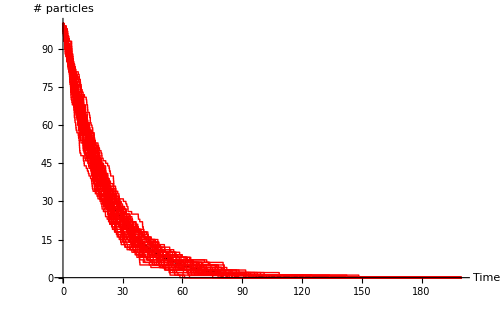

```mathematica
(* Clear function names *)
Clear[plot,ncoords]
(* number of simulations *)
nSim=50;
For[i=0,i≤ nSim,i++,

Clear[n,time]; (* function names for particle number and elapsed time *)
t=0;
γ=0.05; (* decay rate *)
tmaxplot=200; (* maximum elapsed time *)
nInit=100; (* intial particle number *)

time[0]=0;
n[0]=nInit;


While[time[t]<tmaxplot,
(* reaction rates *)
rd=γ n[t]; 
(* exclude possibility its all over *)
If[rd==0, n[t+1]=n[t];time[t+1]=tmaxplot;,
(* time until next event *)
time[t+1]=time[t]-Log[RandomReal[]]/rd; n[t+1]=n[t]-1;];
t=t+1];

(* Make plot for simulation *)
tmax=t;
ncoords[i]=Append[Flatten[Table[{{time[t],n[t]},{time[t+1],n[t]}},{t,0,tmax-1}],1],{time[tmax],n[tmax]}];

plot[i]=ListPlot[ncoords[i],AxesOrigin->{0,0},Joined->True,PlotStyle->{Thickness[0.002],Red},
ImageSize->400,
PlotRange->{{0,tmaxplot},{0,nInit}}];]

(* first moment *)
Clear[n1]
n1[t_]:=nInit Exp[-γ t]; (* mean *)
plotAv=Plot[n1[t],{t,0,tmaxplot},PlotRange->All,PlotStyle->Black,
LabelStyle->{FontFamily->"Helvetica",FontSize->15},
AxesLabel->{"Time","# particles"}];

(* Combine *)
plotMulti=Show[plotAv,Flatten[Table[plot[k],{k,0,nSim}]],ImageSize->500]
```

## Example II : SIS Disease Model

The SIS model captures the dynamics of a disease that does not render immunity to an individual once recovered.

There now exist multiple events that can take place:

The rate at which an individual in the population becomes infected is	ω(s-1,i+1 | s,i) = β s i

The rate at which an individual recovers is	ω(s+1,i-1 | s,i) = γ i

We plot stochastic realisations alongside the solution to the deterministic SIS model for comparison.

```mathematica
(* parameter values *)
pop=100; (* total population size *)
β=0.27/pop; (* infection rate *)
γ=0.2; (* recovery rate *)
```

### Deterministic Analysis

```mathematica
(* Deterministic Equilibrium Solution obtained by solving dI/dt=0 *)
Clear[deriv]
deriv[I_]:=β (pop-I)I-γ I;
sol=Solve[deriv[x]==0,x];
equilibrium=x/.sol[[2]];
```

```mathematica
(* Plot solutions to the DE *)
Clear[y,t];
desol=Table[NDSolve[{y'[t]==deriv[y[t]],y[0]==j},y,{t,0,800}],{j,{10,20,30,50,70}}];
```

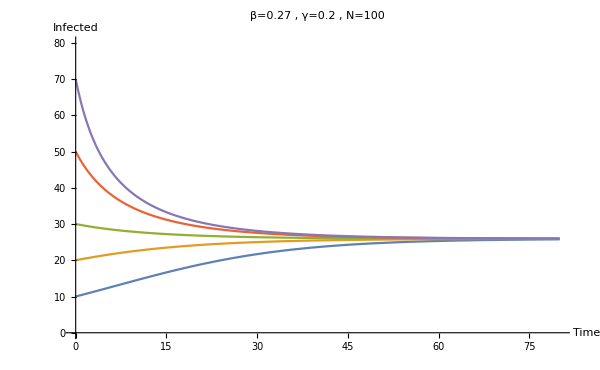

```mathematica
solplot=Plot[Evaluate[y[t]/.desol],{t,0,80},PlotRange->{0,80}, AxesLabel->{Style["Time",TMBFS15],Style["Ιnfected",TMBFS15]},ImageSize->600,PlotLabel->Style["β="<>ToString[β pop] ", γ="<>ToString[γ] ", N="<>ToString[pop],TMBFS15]]
```

### Stochastic Simulation using Gillespie

Let n be the number of infecteds. We assume population size N is constant hence S=N-n.

```mathematica
(* Set up and parameter values *)
Clear[time,n,i];
t=0;
tmaxplot=1000;
time[0]=0;
n[0]=70;

(* Deterministic Equilibrium Solution obtained by solving dI/dt=0 *)
sol=Solve[i^2+i(γ/β + ϵ-pop)-pop ϵ ==0,i];
equilibrium=i/.sol[[2]];

(* Begin Gillespie *)
While[time[t]<tmaxplot,

(* set rates for this iteration *)
rb=β(pop-n[t])(n[t]+ϵ); rd=γ n[t]; rtot=rb+rd;
(* exclude possibility it is all over *)
If[rtot==0,n[t+1]=n[t]; time[t+1]=tmaxplot;,
(* time till next event *)
time[t+1]=time[t] - Log[RandomReal[]]/rtot; rt=RandomReal[];
(* update event *)
n[t+1]=n[t]+Which[rt<rb/rtot, 1,True,-1]];
t=t+1;];


(* Plot the simulation *)
tmax=t;
ncoords=Append[Flatten[Table[{{time[t],n[t]},{time[t+1],n[t]}},{t,0,tmax-1}],1],{time[tmax],n[tmax]}];

TMBFS20={FontFamily->"Helvetica",FontSize->20};

legend=PointLegend[{Blue,Red},{Style["deterministic solution",TMBFS20],Style["stochastic simulation",TMBFS20]}];

sim=Show[Plot[Evaluate[y[x]/.desol[[5]]],{x,0,tmaxplot},PlotRange->{{0,tmaxplot},{0,80}}],
ListPlot[ncoords,AxesOrigin->{0,0},Joined->True,PlotStyle->{Thickness[0.002],Red},PlotLegends->Placed[legend,{{1,1},{1,2}}]],
AxesLabel->{Style["Time",TMBFS20],Style["# Infected",TMBFS20]},
PlotLabel->Style["β="<>ToString[β pop] ", γ="<>ToString[γ] ", N="<>ToString[pop],TMBFS20],PlotRange->{{0,tmaxplot},{0,80}},
ImageSize->600
]
```

-Graphics-